```mathematica
<<MultivariateStatistics`
```

```mathematica
detailIDdr={{AL, AK, AZ, AR, CA, CO, CT, DC, DE,FL,GA,HI,ID,IL,IN,IA,KS,KY,LA,ME,MD,MA,MI,MN,MS,MO,MT,NE,NV,NH,NJ,NM,NY,NC,ND,OH,OK,OR,PA,RI,SC,SD,TN,TX,UT,VT,VA,WA,WV,WI,WY},{416468,416471,416484,416491,416498,416505,416508,416623,416511,417861,416514,416520,416523,416532,416542,416545,416554,416557,416560,416569,416584,416593,416599,416602,416612,416619,416487,416490,416496,416502,416516,416526,416529,416534,416539,416548,416551,416590,416595,416605,416608,416611,416617,416632,416636,416639,416642,416645,416648,416653,416654},
{416469,416472,416485,416493,416500,416506,416509,416624,416512,417866,416515,416521,416524,416537,416543,416546,416555,416558,416561,416570,416585,416594,416600,416603,416614,416621,416488,416492,416497,416503,416518,416527,416530,416535,416540,416549,416552,416591,416597,416606,416609,416613,416618,416634,416637,416640,416643,416646,416649,416651,416655}};
```

```mathematica
ev=Import["http://www.electoral-vote.com/evp2008/Pres/Excel/today.csv"];
```

```mathematica
datad=Table[Drop[Import["http://data.intrade.com/graphing/jsp/downloadClosingPrice.jsp?contractId="<>ToString[detailIDdr[[2,i]] ]],1],{i,51}];
```

```mathematica
datar=Table[Drop[Import["http://data.intrade.com/graphing/jsp/downloadClosingPrice.jsp?contractId="<>ToString[detailIDdr[[3,i]] ]],1],{i,51}];
```

```mathematica
datad[[5,664,2;;-1]]=datad[[5,663,2;;-1]](*data error: CA price on 9.11=3 instead of 91.2*)
```

{91.2,91.2,91.2,91.2,0}

```mathematica
datar[[23,657,2;;-1]]=datar[[23,656,2;;-1]]
```

{38.5,36.2,40,39.9,35}

```mathematica
history=Table[,{2},{30}];
```

```mathematica
closed=datad[[All,All,5]];
closer=datar[[All,All,5]];
window=90;window1=window+1;
```

```mathematica
For[h=1,h≤24,h++,
daysago=h;

returnsd=Table[Log[closed[[i,j-1]]/closed[[i,j]]],{i,51},{j,-window-daysago,-1-daysago}];
returnsr=Table[Log[closer[[a,b-1]]/closer[[a,b]]],{a,51},{b,-window-daysago,-1-daysago}];
cvard=Table[,{51},{51}];cvarr=Table[,{51},{51}];
For[d=1,d≤51,d++,
For[c=1, c≤51, c++, cvard[[d,c]]=Covariance[returnsd[[c]],returnsd[[d]] ];
cvarr[[d,c]]=Covariance[returnsr[[c]],returnsr[[d]] ]
]];
timeleft=DateDifference[DateList[][[1;;3]],{2008,11,4}]+daysago;
closed2=Table[closed[[e,-window-daysago;;-1-daysago]],{e,51}];
closer2=Table[closer[[f,-window-daysago;;-1-daysago]],{f,51}];
simsdet=Table[
ds=Exp[Transpose[RandomReal[MultinormalDistribution[Table[0,{51}],cvard],timeleft]]];
rs=Exp[Transpose[RandomReal[MultinormalDistribution[Table[0,{51}],cvarr],timeleft]]];
endd=closed2[[All,-1]];
endr=closer2[[All,-1]];
For[g=1,g≤51,g++,Do[endd[[g]]=endd[[g]] ds[[g,z]];endr[[g]]=endr[[g]] rs[[g,z]],{z,timeleft}]];
chanced=endd/(endd+endr);
Table[If[chanced[[y]]>.5,ev[[2;;-2,2]][[y]],0],{y,51}],{500}
];
sims=Map[Total,simsdet];
history[[1,h]]=Count[sims,n_/;n>268]/Length[sims]//N;
history[[2,h]]=Mean[sims]//N;
Print[h]
]
```

```mathematica
history
```

{{0.914,0.868,0.804,0.774,0.74,0.744,0.774,0.764,0.544,0.45,0.45,0.452,0.376,0.456,0.548,0.576,0.548,0.702,0.884,0.906,0.858,0.882,0.862,0.822,Null,Null,Null,Null,Null,Null},{302.822,291.182,286.398,283.634,282.214,285.512,284.28,283.832,268.406,264.916,263.736,264.984,261.148,262.976,269.556,272.008,270.046,278.7,292.188,294.422,292.228,296.092,292.724,288.576,Null,Null,Null,Null,Null,Null}}

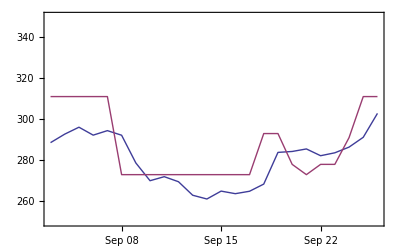

```mathematica
DateListPlot[{Reverse[Take[history[[2]],24]],Reverse[Take[winning,24]]},{2008,9,3},Joined->True,PlotRange->{Automatic,{250,350}}]
```

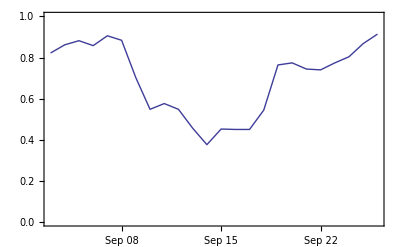

```mathematica
DateListPlot[Reverse[Take[history[[1]],24]],{2008,9,3},Joined->True,PlotRange->{Automatic,{0,1}}]
```

```mathematica
(*For some reason, covariance matrix is problematic 25 days ago & more*)
```

```mathematica
hist2=Table[,{2},{60}];hist2[[All,1;;30]]=history;
```

```mathematica
For[h=25,h≤Length[hist2[[1]]],h++,
daysago=h;

returnsd=Table[Log[closed[[i,j-1]]/closed[[i,j]]],{i,51},{j,-window-daysago,-1-daysago}];
returnsr=Table[Log[closer[[a,b-1]]/closer[[a,b]]],{a,51},{b,-window-daysago,-1-daysago}];
cvard=Table[,{51},{51}];cvarr=Table[,{51},{51}];
For[d=1,d≤51,d++,
For[c=1, c≤51, c++, cvard[[d,c]]=Covariance[returnsd[[c]],returnsd[[d]] ];
cvarr[[d,c]]=Covariance[returnsr[[c]],returnsr[[d]] ]
]];
timeleft=DateDifference[DateList[][[1;;3]],{2008,11,4}]+daysago;
closed2=Table[closed[[e,-window-daysago;;-1-daysago]],{e,51}];
closer2=Table[closer[[f,-window-daysago;;-1-daysago]],{f,51}];
simsdet=Table[
ds=Exp[Transpose[RandomReal[MultinormalDistribution[Table[0,{51}],cvard+.000001],timeleft]]];
rs=Exp[Transpose[RandomReal[MultinormalDistribution[Table[0,{51}],cvarr+.000001],timeleft]]];
endd=closed2[[All,-1]];
endr=closer2[[All,-1]];
For[g=1,g≤51,g++,Do[endd[[g]]=endd[[g]] ds[[g,z]];endr[[g]]=endr[[g]] rs[[g,z]],{z,timeleft}]];
chanced=endd/(endd+endr);
Table[If[chanced[[y]]>.5,ev[[2;;-2,2]][[y]],0],{y,51}],{500}
];
sims=Map[Total,simsdet];
hist2[[1,h]]=Count[sims,n_/;n>268]/Length[sims]//N;
hist2[[2,h]]=Mean[sims]//N;
Print[h]
]
```

```mathematica
datad[[1,-1,1]]
```

Oct 1, 2008

```mathematica
hist2[[1]]=Prepend[hist2[[1]],.985]
hist2[[2]]=Prepend[hist2[[2]],323.1]
```

{0.985,0.988,0.968,0.974,0.938,0.914,0.868,0.804,0.774,0.74,0.744,0.774,0.764,0.544,0.45,0.45,0.452,0.376,0.456,0.548,0.576,0.548,0.702,0.884,0.906,0.858,0.882,0.862,0.822,0.784,0.794,0.81,0.736,0.688,0.676,0.814,0.822,0.788,0.816,0.792,0.742,0.76,0.82,0.854,0.836,0.868,0.87,0.888,0.896,0.902,0.866,0.858,0.866,0.904,0.88,0.89,0.91,0.924,0.932,0.878,0.94,0.916,0.912,0.912,0.92}

{323.1,322.4,315.8,315.4,303.72,302.822,291.182,286.398,283.634,282.214,285.512,284.28,283.832,268.406,264.916,263.736,264.984,261.148,262.976,269.556,272.008,270.046,278.7,292.188,294.422,292.228,296.092,292.724,288.576,281.896,285.224,284.198,279.236,277.14,275.216,285.68,286.162,284.318,286.728,283.296,281.724,281.71,287.018,290.998,289.57,293.712,293.438,296.008,296.652,295.996,294.398,294.248,293.816,301.154,295.912,298.954,303.58,311.372,307.07,303.828,309.386,308.52,306.87,308.974,308.52}

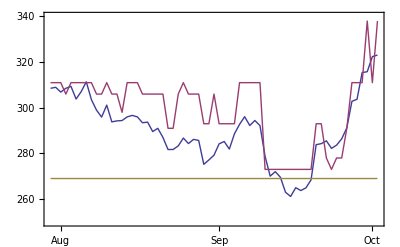

```mathematica
DateListPlot[{Reverse[hist2[[2]]],Reverse[Take[winning,65]],Table[269,{65}]},{2008,7,30},Joined->True,PlotRange->{Automatic,{250,340}}]
```

```mathematica
natr=Import["http://data.intrade.com/graphing/jsp/downloadClosingPrice.jsp?contractId=376101"];
natd=Import["http://data.intrade.com/graphing/jsp/downloadClosingPrice.jsp?contractId=409933"];
```

```mathematica
chancend=Take[natd[[All,5]],-300]/(Take[natd[[All,5]],-300]+Take[natr[[All,5]],-300]);
```

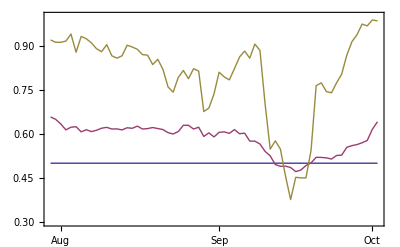

```mathematica
DateListPlot[{Table[.5,{65}],chancend[[-65;;-1]],Reverse[hist2[[1]]]},{2008,7,30},Joined->True,PlotRange->{Automatic,{.3,1}}]
```